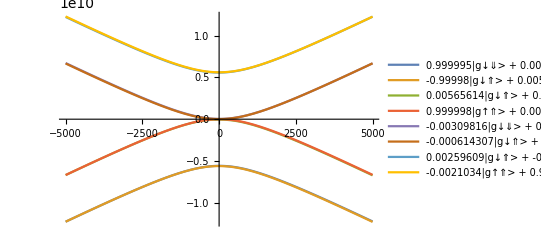

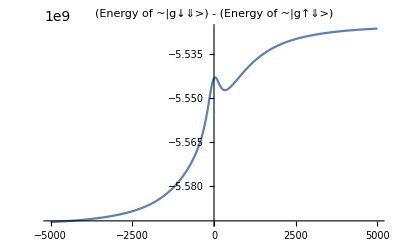

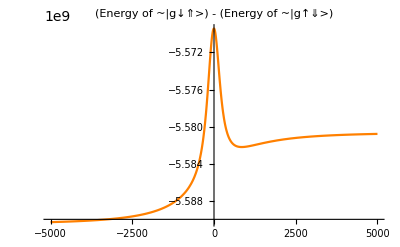

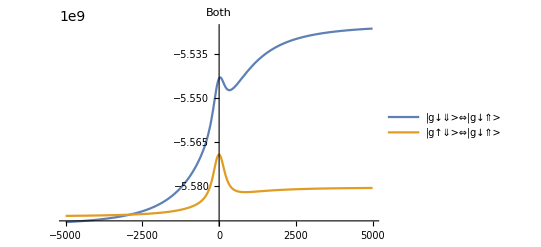

```mathematica
(* Plot energy transitions in the lab frame *)

(* find H in GE basis *)
HinGE = transform[H, UtoGE] // FullSimplify;

(* define constants *)
setVariables[];

Bac = 0;

ϵ0 /. {ΔE -> 0};

energiesAt[Ef_] := Eigensystem[HinGE /. {ΔE -> Ef}][[1]]
statesAt[Ef_] := Eigensystem[HinGE /. {ΔE -> Ef}][[2]]
systemAt[Ef_] := Eigensystem[HinGE /. {ΔE -> Ef}]
energiesAtZero = energiesAt[0];

(*targetStates = {{0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 1, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}};*)
targetStates = IdentityMatrix[8];

order[Ef_] := Table[Ordering[row, -1][[1]], {row,Abs[targetStates.ConjugateTranspose[statesAt[Ef]]]}]

statesAtZero = statesAt[0];

(* plot all 8 energies colored by their states' main component *)
Plot[
{
energiesAt[Ef][[order[Ef][[1]]]],
energiesAt[Ef][[order[Ef][[2]]]],
energiesAt[Ef][[order[Ef][[3]]]],
energiesAt[Ef][[order[Ef][[4]]]],
energiesAt[Ef][[order[Ef][[5]]]],
energiesAt[Ef][[order[Ef][[6]]]],
energiesAt[Ef][[order[Ef][[7]]]],
energiesAt[Ef][[order[Ef][[8]]]]
},
 {Ef, -5000, 5000},
PlotLegends->Table[stateString[statesAtZero[[i]], basisGE, .0001], {i, order[0]}]
]

(* plot nuclear spin transition *)
pNSpin = Plot[
{
energiesAt[Ef][[order[Ef][[1]]]] - energiesAt[Ef][[order[Ef][[3]]]]
},
 {Ef, -5000, 5000},
PlotLabel->"(Energy of ~"<>basisGE[[1]]<>") - (Energy of ~"<>basisGE[[3]]<>")"
]

(* plot flip flop transition *)
pFF = Plot[
{
energiesAt[Ef][[order[Ef][[2]]]] - energiesAt[Ef][[order[Ef][[3]]]]
},
 {Ef, -5000, 5000},
PlotLabel->"(Energy of ~"<>basisGE[[2]]<>") - (Energy of ~"<>basisGE[[3]]<>")",
PlotRange->All,
PlotStyle->Orange
]

Plot[
{
energiesAt[Ef][[order[Ef][[1]]]] - energiesAt[Ef][[order[Ef][[3]]]],
energiesAt[Ef][[order[Ef][[2]]]] - energiesAt[Ef][[order[Ef][[3]]]]
},
 {Ef, -5000, 5000},
PlotLabel->"Both",
PlotLegends->{"|g↓⇓>⇔|g↓⇑>", "|g↑⇓>⇔|g↓⇑>"}
]


clearVariables[];
```

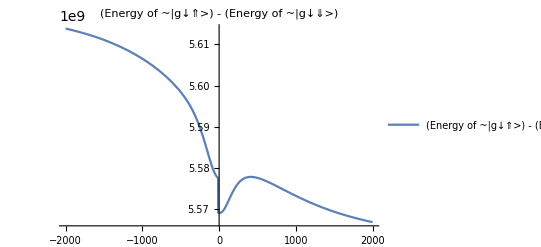

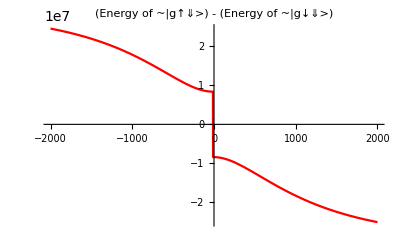

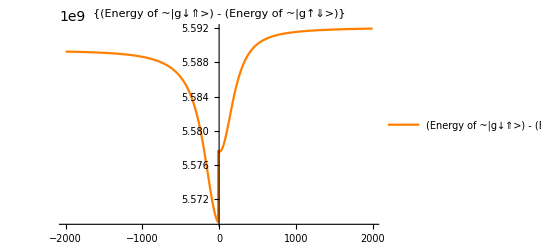

OptionValue::nodef: Unknown option PlotLegends for Graphics.

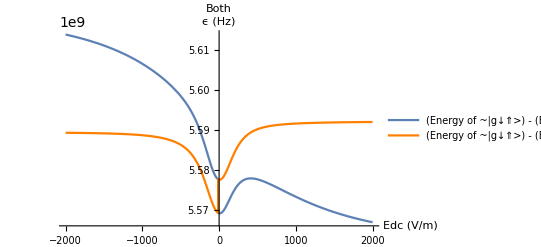

{-0.000521228,-0.466385,-0.000252091,0.232458,0.201038,-0.00313115,0.829471,0.000606383}

```mathematica
(* Plot energy transitions in the rotating frame *)

(* Urot = MatrixExp[ⅈ*2*π*νB*t*(TProduct[σI, σI, Sz] + TProduct[σI, Iz, σI])]; *)

(* find H in GE basis *)
(* HinGE = transform[H, UtoGE] // FullSimplify; *)


(* take Hns with the RWA already used *)
Hns = δB*TProduct[σI, Sz, σI] - (γn*B0 + νB)*TProduct[σI, σI, Iz] + (Bac/2)(γe*TProduct[σI, Sx, σI] - γn*TProduct[σI, σI, Ix]) + Horb + HA;
(* transform to GE basis *)
HnsInGE = transform[Hns, UtoGE] // FullSimplify;



setVariables[];

B0 = -1*B0;
(* set Bac *)
Bac = .0006;
Vt = Vt*1;
νB = νB*1;

energiesAt[Ef_] := Eigensystem[HnsInGE /. {ΔE -> Ef}][[1]]
(*energiesAt[Ef_] := statesAt[Ef].(HnsInGE /. {ΔE -> Ef, t->0}).ConjugateTranspose[statesAt[Ef]] // Diagonal*)
statesAt[Ef_] := Eigensystem[HnsInGE /. {ΔE -> Ef}][[2]]
systemAt[Ef_] := Eigensystem[HnsInGE /. {ΔE -> Ef}]
energiesAtZero = energiesAt[0];

targetStates = IdentityMatrix[8];
order[Ef_] := Table[Ordering[row, -1][[1]], {row,Abs[targetStates.ConjugateTranspose[statesAt[Ef]]]}]

statesAtZero = statesAt[0];

pNSpin = Plot[
{
energiesAt[Ef][[order[Ef][[2]]]] - energiesAt[Ef][[order[Ef][[1]]]]
},
 {Ef, -2000, 2000},
(*ColorFunction-> Function[
{x, y}, ColorData["Rainbow"][
Abs[
statesAt[x][[1]][[1]]
]
]
],*)
PlotLabel->"(Energy of ~"<>ToString[basisGE[[2]]]<>") - (Energy of ~"<>ToString[basisGE[[1]]]<>")",
PlotLegends->{"(Energy of ~"<>ToString[basisGE[[2]]]<>") - (Energy of ~"<>ToString[basisGE[[1]]]<>")"}
]

Plot[
{
energiesAt[Ef][[order[Ef][[3]]]] - energiesAt[Ef][[order[Ef][[1]]]]
},
 {Ef, -2000, 2000},
PlotLabel->"(Energy of ~"<>ToString[basisGE[[3]]]<>") - (Energy of ~"<>ToString[basisGE[[1]]]<>")",
PlotStyle->Red
]

pFF = Plot[
{
energiesAt[Ef][[order[Ef][[2]]]] - energiesAt[Ef][[order[Ef][[3]]]]
},
 {Ef, -2000, 2000},
PlotLabel->{"(Energy of ~"<>ToString[basisGE[[2]]]<>") - (Energy of ~"<>ToString[basisGE[[3]]]<>")"},
PlotRange->All,
PlotStyle->Orange,
PlotLegends->{"(Energy of ~"<>ToString[basisGE[[2]]]<>") - (Energy of ~"<>ToString[basisGE[[3]]]<>")"}
]

Show[pNSpin, pFF, PlotRange-> All, PlotLabel->"Both", AxesLabel->{"Edc (V/m)", "ϵ (Hz)"}, PlotLegends->{
"(Energy of ~"<>ToString[basisGE[[2]]]<>") - (Energy of ~"<>ToString[basisGE[[1]]]<>")",
"(Energy of ~"<>ToString[basisGE[[2]]]<>") - (Energy of ~"<>ToString[basisGE[[3]]]<>")"
}]

statesAt[0][[order[0][[7]]]]

(*Urot // MatrixForm*)

clearVariables[];
```

```mathematica
HinGE /. {ΔE -> 0, t->0} // MatrixForm
```

(-5.51585×10^7 | 0. | 0. | 0. | -1.7422×10^7 | 0. | 0. | 0.
0. | -8.09625×10^7 | 2.925×10^7 | 0. | 0. | 1.1828×10^7 | -2.925×10^7 | 0.
0. | 2.925×10^7 | -5.684×10^9 | 0. | 0. | -2.925×10^7 | 1.7422×10^7 | 0.
0. | 0. | 0. | -5.65131×10^9 | 0. | 0. | 0. | -1.1828×10^7
-1.7422×10^7 | 0. | 0. | 0. | 5.68056×10^9 | 0. | 0. | 0.
0. | 1.1828×10^7 | -2.925×10^7 | 0. | 0. | 5.65475×10^9 | 2.925×10^7 | 0.
0. | -2.925×10^7 | 1.7422×10^7 | 0. | 0. | 2.925×10^7 | 5.17125×10^7 | 0.
0. | 0. | 0. | -1.1828×10^7 | 0. | 0. | 0. | 8.44085×10^7)

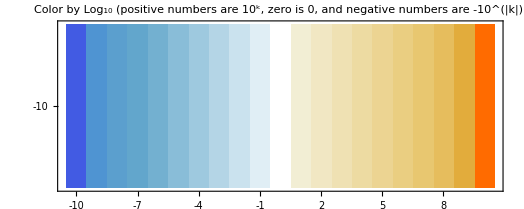

MatrixPlot::mat0: Argument HinGE at position 1 is not a matrix.

```mathematica
data = Table[10^Abs[i]*Sign[i], {i, -10, 10}]*Max[HinGE /. {ΔE -> 0}]/10^10;
MatrixPlot[{data}, FrameTicks-> {Table[{i + 11, i}, {i, -10, 10}]}, PlotLabel->"Color by Log_10 (positive numbers are 10^k, zero is 0, and negative numbers are -10^(|k|))"]
Manipulate[
MatrixPlot[
HinGE /. {ΔE -> Ef}, FrameTicks->{
{Table[{i, basisGE[[i]]}, {i, Length[HinGE]}], Table[{i, basisGE[[i]]}, {i, Length[HinGE]}]},
{Table[{i, basisGE[[i]]}, {i, Length[HinGE]}], Table[{i, basisGE[[i]]}, {i, Length[HinGE]}]}
}
]
, {Ef, Table[i*500, {i, -10, 10}]}
]
```